# Mathematica Notes

## Misc. & general

Dr. Liu Haohui

## Environment setting & working

#### setting working directory, need to make sure folder exist

```mathematica
SetDirectory[FileNameJoin[{$UserDocumentsDirectory,"Mathematica"}]];
SetDirectory[NotebookDirectory[]];
```

#### append external search path

```mathematica
AppendTo[$Path,"Z:\\05 Data\\01 Sunspectra\\SINGAPORE SPECTRUM DATA\\Raw spectrum data"];
```

#### Storing intermediate files / data / expressions / definitions

use Put (>>) to store values of variables and Get (<<) to retrieve them

```mathematica
{a,data}>>testData3;
Put[{a,data},FileNameJoin[{$UserDocumentsDirectory,"testData"}]];

{b,data2}=<<testData3;
```

use Save to store delayed definition of variables

```mathematica
f[x_] := x^2;
Save["varDef",f];
```

## Function definition

#### Naming of variables/functions

Other types of eligible naming (other than usual ones like varNum1) include: 
indexed (or subscripted) variables (with number or strings or symbols). However these things are NOT symbols if no values are assigned to them, in that case they have heads as defined before []. DO NOT assign values to the headings (make sure they are free of values). 
All of these variables with the same head label only needs to be defined as local variable once in Module.

```mathematica
var["key a"]=1;
var[1]=a+b;
area[square]=2;
```

$ sign, some letter like forms, such as Esc+_+Esc (LetterSpace), which gives a light underscore, or Esc+u[+Esc (UnderBracket). Seems that some do not work, so choose with care.

```mathematica
var a=1;
var⎵b=1;
var$a=1;
```

using scripts to define numerous variables is possible:

```mathematica
Evaluate[Symbol["t"<>"1"]]=3;
t1+3
```

6

#### Skills with patterns and definitions

Use patterns and delayed definition, and Module (if needed) to define functions.

```mathematica
(* define objects to be passed out, working but probably problematic *)
inspect[a_]:=Module[{window,size},size=Dimensions[a][[1]];
window=Manipulate[a[[r]],{r,1,size,1}];
window]
```

the context of these variables above are messy, not sorted out yet...

Default parameter values can be initiated in function definition.

```mathematica
ftest[x_:2,y_:3]:=Module[{output=1},Return[{output*x,output*y}]]
```

```mathematica
ftest[]
```

{2,3}

```mathematica
ftest[5]
```

{5,3}

```mathematica
ftest[1,5]
```

{1,5}

Stipulate conditions and restrictions for input variables.

```mathematica
f[x_Integer]:=x*2;
f[x_?Positive]:=x*2;
fac[n_/;n>0]:=n!;  (* added constraint for input variable, equivalent to above *)
w[x_,y_]:=p[x]/;y==1-x; (* added restriction in the body of function definition *)
```

Define function with composite brackets of inputs

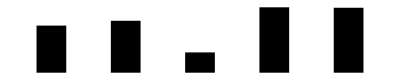

```mathematica
bar[w_][h_,{p_}]:=Rectangle[{p-w/2,0},{p+w/2,h}];

bar[0.4]~MapIndexed~RandomReal[1,5]//Graphics
```

#### Functions with options

```mathematica
Options[f]={Option1->0};
f[a_,opt:OptionsPattern[]]:=Module[{out},
out=Solve[a+1+OptionValue[Option1]==0,a]
]
f[y,Option1->y]
```

{{y→-1/2}}

Caution: when passing in expressions as options (trying to stitch a foreign piece to modify the equation), the symbol may conflict with local variable. For example, the following will not properly evaluate, removing t from the list of local variables solves the problem.

```mathematica
Options[f]={Option1->0};
f[a_,opt:OptionsPattern[]]:=Module[{out,localF,t},
localF=FindRoot[a+#+OptionValue[Option1]+Exp[t]==0,{t,-1}]&;
{t/.(localF@1)}
]
f[0,Option1->t*2]
```

OptionPattern can be passed on to inner functions.

```mathematica
modListPlot[x_,o:OptionsPattern[]]:=ListPlot[Reverse/@x,o]
(*effectively reversed the x and y axis*)
```

#### Misc. tips

Can functions use global variables without specifying them as input? 
--- seems to be yes, make sure the value at the time of function execution is correct.

Modules need to end with some returned value or Return[] if nothing is returned. Use Return[{var1,var2}] to return multiple variables.

Define function in a way that it remembers its last call:

```mathematica
function[input_]:=function[input]=Module[{},input!];
```

Pure function that only operates on the first argument:

```mathematica
f=Length@#1&;
f[{1,2,3}]
f[{1,2,3},2,3,4]
```

## Matrix and list manipulation

## Basics

Generate test lists or arrays:

```mathematica
m=Array[10#1+#2&,{3,4}];
MatrixForm@m
```

(11 | 12 | 13 | 14
21 | 22 | 23 | 24
31 | 32 | 33 | 34)

```mathematica
n=RandomInteger[9,{6,4}];
MatrixForm@n
```

(8 | 7 | 8 | 5
3 | 4 | 4 | 6
0 | 4 | 2 | 6
7 | 8 | 3 | 1
7 | 7 | 8 | 2
1 | 6 | 4 | 1)

Combine two vectors in columns:
Bracket two vectors (lists) like {list1, list2} combine them row to row, transpose to combine them column to column, or use Thread.

```mathematica
Transpose[{list1,list2}];
Thread[{list1,list2}];
```

Horizontal and vertical concatenation of two matrices : use Join; 
If needed, transform (row) vector into column vector using List.

```mathematica
column1=List/@vector1;
Join[matrix1,column1,2]; (* appends column1 to the right of matrix1 *)
```

Alternatively, use this:

```mathematica
MapThread[Append,{matrix1,vector1}]; (* appends vector1 to the right of matrix1 as an additional column *)
```

Insert a column:

```mathematica
Insert[matrix1//Transpose,vector1,2]//Transpose
```

Adding/minus rows/columns, swapping rows/columns (operation on columns):
can be done by directly setting values on picked parts.

```mathematica
matrix1[[All,3]]+=matrix2[[All,1]]; (* column 3 = column 3 + column 1 of matrix 2*)
matrix1[[3]]-=matrix2[[1]];
```

```mathematica
matrix[[{1,3}]]=matrix[[{3,1}]]; (* swap row 1 and 3 *)
matrix[[All,{1,3}]]=matrix[[All,{3,1}]]; (* swap column 1 and 3 *)
```

Multiplying/divide rows / columns

```mathematica
matrix*{1,2,1,1}; (* Multiply row 2 with 2 *)
matrixᵀ*{1,2,1,1}//Transpose;  (* Multiply column 2 with 2 *)
```

delete row/column
use Drop or Part ([[ ]]) operation

```mathematica
Drop[m,{2}]//MatrixForm
```

(11 | 12 | 13 | 14
31 | 32 | 33 | 34)

```mathematica
Delete[m,2]
```

{{11,12,13,14},{31,32,33,34}}

```mathematica
Drop[m,None,{2}]//MatrixForm
```

(11 | 13 | 14
21 | 23 | 24
31 | 33 | 34)

Assign new values to a row/column

```mathematica
m[[All,2]]={1,2,3};
MatrixForm@m
```

(11 | 1 | 13 | 14
21 | 2 | 23 | 24
31 | 3 | 33 | 34)

```mathematica
m[[All,2;;3]]={{1,2},{3,4},{5,6}};
MatrixForm@m
```

(11 | 1 | 2 | 14
21 | 3 | 4 | 24
31 | 5 | 6 | 34)

## Boolean masking

Extract corresponding elements from two lists

```mathematica
list1={1,2,3};
list2={4,5,6};
var1=Extract[list1,Position[list2,n_/;n==Max[list2]]];
(*this gives a list, so var 1 is a list. To extract the value, use: *)
var1=Extract[list1,First@Position[list2,n_/;n==Max[list2]]];
```

## String & file manipulation

Get the list of all file names in a directory:

```mathematica
FileNames[__~~".txt",dataDir];
FileNames["2014"~~__~~".txt",dataDir];
```

This returns a list of strings CONTAINING file path before the file name (aboslute file names) when data directory is specified, if don’t want file path before, use FileNameTake or SetDirectory to folder containing the file, if don’t want extension either, use FileBaseName

Pick out just the file name without extensions:

```mathematica
FileBaseName[fileName];
```

Join and creat new file names from parts of other file names:

```mathematica
FileNameJoin[{dataDir,StringCases[fileName,"Denver"~~x__~~"meta"->x][[1]]<>".txt"}]
```

StringCases returns a list, so need to take the string out using Part [[ ]]. 
It is good to use this intead of joining strings as it will add \ before file name.

Define string patterns with specified characters:

```mathematica
(* results returned contain the whitespace characters *)
StringCases["it is 200 and 30",Whitespace~~DigitCharacter..~~Whitespace]
```

Other special characters that are useful: WordBoundary.

Select from a list of strings ones containing certain words:

```mathematica
Select[{"asb","ddg","ab_wordOfInterest","dummy"},StringContainsQ[#,"wordOfInterest"]&]
```

{ab_wordOfInterest}

## Advanced language techniques & features

## Use of pattern test

Use pure function forms as test:

```mathematica
ReplacePart[{1,2,3,4,5},_?(#>2&)->10];
```

Pattern test _? (or just ?) can be used with any function that gives True or False as logical outputs.

Pattern test elements can be combined:

```mathematica
Position[<|"a"->1,"b"->2,"c"->3,"d"->4|>,_Integer?PrimeQ]
```

## Applying complicated functions to complicated arguments

### Use Map family functions to apply functions.

Use Thread or MapThread to do the trick of applying in situations when arguments are separately grouped, but there can be some problems using Thread as function inside Thread is evaluated before being threaded:

```mathematica
Thread[{#1,#2}&[{a,b},{c,d}]]
```

{{a,c},{b,d}}

```mathematica
Thread[{{#1,1},#2}&[{a,b},{c,d}]]
```

{{{a,b},c},{1,d}}

First one apparently gives the correct answer, but second one doesn’t give intended output. This is because pure function (expected two arguments) is evaluated before passing the output to function Thread, resulting in Thread[{{a,b},1},{c,d}], which is just threading function List to the two sublists. 

When function can be evaluated, use MapThread instead to give correct output.

```mathematica
MapThread[{{#1,1},#2}&,{{a,b},{c,d}}]
```

{{{a,1},c},{{b,1},d}}

When mapping or using MapAt, if there is composite functions that need to apply one after another, use Composition (@*) to do so:

```mathematica
Map[g[f],{a,b,s}]
```

{g[f][a],g[f][b],g[f][s]}

```mathematica
Map[l@g[f],{a,b,s}]
```

{l[g[f]][a],l[g[f]][b],l[g[f]][s]}

```mathematica
(* above two do not give desired output *)
Map[l@*g@*f,{a,b,s}]
```

{l[g[f[a]]],l[g[f[b]]],l[g[f[s]]]}

Alternative is to use RightComposition (/*) to concatenate functions:

```mathematica
f/*g/*h@x
```

h[g[f[x]]]

### Use slot sequence:

```mathematica
Join[##,2]&@@{a,b}
```

Join[a,b,2]

## Symbolic manipulation of codes themselves & meta-programming

Use ToExpression to script reference to variables (without the need to specifically write out the variable name in the code):

```mathematica
Table[Evaluate[ToExpression["variable$"<>ToString[i]]]=i,{i,10}];
(* but this can be equivalently done by: *)
Table[variable[i]=i,{i,10}];
```

Take note when puting Evaluate into a function argument that doesn’t get evaluated first (?), or a symbol is first evaluated to become its value assigned to it, there will be a problem, the variable is not generated during the operation. For example, in:

```mathematica
Put[Evaluate[ToExpression["test"]],"test"]; 
{Evaluate[ToExpression["test"<>"1"]],Evaluate[ToExpression["test"<>"2"]]}={1,2};
(* error! *)
```

In general, this method works if it is first time assignment of value to a symbol, i.e. there is not yet any value associated with the symbol yet. But later reference to the symbol itself when it contains a value is not possible. This affects cases when one wants to reassign a new value to the symbol. One has to resort to explicitly writing out its name in the codes.

```mathematica
Evaluate@ToExpression["var"<>"1"]=1
```

1

```mathematica
var1
```

1

```mathematica
Evaluate@ToExpression["var"<>"1"]=1
```

Set::setraw: Cannot assign to raw object 1.

1

## Misc.

Sometimes feeding a list to a function return a list of results, sometimes no (list is treated as THE input object). Ways to tell? 
When does a function return the desired result in a list (inside an additional bracket {}), when does it return it in itself?

## Useful packages

## Mathematica for Prediction

```mathematica
Import["https://raw.githubusercontent.com/antononcube/MathematicaForPrediction/master/MathematicaForPredictionUtilities.m"];
```